```mathematica
Exit[]
```

```mathematica
$Assumptions=μ≥0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
u[W_]:=Exp[-γ W]
pr[B_]:=ⅇ^(-B^2/2)/√(2 π)
σ2t=(.2)^2.5;xx[B_]:=Exp[ Sqrt[σ2t] B-σ2t/2];
NIntegrate[xx[B]pr[B],{B,-∞,∞}]-1
σ2t=.;
c[x_]:=If[x==0,0,.001]+Abs[x].00025
```

-5.0826×10^-13

```mathematica
g[0,h_,P_]:=Max[P,0]+c[h]
g[n_,h_,P_]:=Table[
```

```mathematica
f[n_,h_,P_,ψ_,ϕ_]:=ex[n,P,ψ,ϕ]+c[h-ψ]
```

```mathematica
ex[n_,P_,ψ_,ϕ_]:=ex[n,P,ψ,ϕ]=
```

# Old shit

Short put

```mathematica
γ=.01;μ=0;t=1;k=550;S0=600;σ=.25;
put[W_]:=Max[0,k-W]
FinancialDerivative[{"European","Put"}, {"StrikePrice"-> k, "Expiration"->t},{"InterestRate"-> 0.0, "Volatility" -> σ, "CurrentPrice"-> S0, "Dividend"->0}]
p=NIntegrate[put[xx[B]]pr[B],{B,-∞,∞}]

q=Log[NIntegrate[u[-put[xx[B]]]pr[B],{B,-∞,∞}]]/γ
```

35.6083

35.6083

58.5032

Revision

```mathematica
γ=.01;k=550;S0=600;σSqrtT=.25;

p0=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> k, "Expiration"->1},{"InterestRate"->0, "Volatility" -> σSqrtT, "CurrentPrice"-> S0}];

density[B_]:=ⅇ^(-B^2/2)/√(2 π)
put[B_]:=Max[0,k-S0 Exp[ σSqrtT B- σSqrtT^2/2]]
p1=NIntegrate[put[B]density[B],{B,-∞,∞}];
p2=1/γ Log[NIntegrate[Exp[γ put[B]]density[B],{B,-∞,∞}]];
{p0,p1,p2}
```

{35.6083,35.6083,58.5032}

Marginal utility-based price

```mathematica
μT=-0.08;
put[B_]:=Max[0,k-S0 Exp[ σSqrtT B+μT -σSqrtT^2/2]]
pP=NIntegrate[put[B]density[B],{B,-∞,∞}]

pP0=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> k, "Expiration"->1},{"InterestRate"->0, "Dividend"-> -μT,"Volatility" -> σSqrtT, "CurrentPrice"-> S0}]
g[v_]:=-1/γ Log[NIntegrate[Exp[-γ v put[B]]density[B],{B,-∞,∞}]];
```

52.9911

52.9911

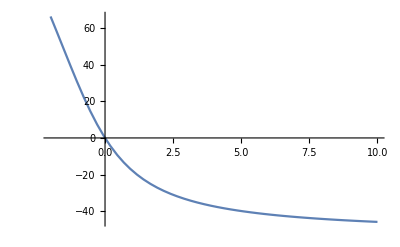

```mathematica
Plot[{g[v]/v-pP},{v,-2,10}]
```